# 🌈 Runge-Kutta 4th Order Method (RK4) 🌈 ✍️ Created by Haroon Sakhi

## ✨ Introduction

The Runge-Kutta 4th Order Method (RK4) is a widely used numerical method for solving differential equations due to its accuracy and efficiency. This notebook provides:

📌 A concise mathematical formulation of RK4.
📌 Step-by-step implementation.
📌 A Mathematica code to compute RK4.
📌 A comparison with Euler’s method.

"💡 Key Insight: RK4 is more accurate than Euler's method because it computes four intermediate slopes."

### 🔢 Proof

Consider the first-order differential equation:

with an initial condition:

The goal is to approximate  using a fourth-order method.

#### Taylor Series Expansion

The exact value of   at    can be written as a Taylor series:

Since the equation is given as   , the next step is to compute higher derivatives of   to get a more accurate approximation.

#### Computing Higher Derivatives

Expanding each term:

First derivative:

Second derivative:

Third derivative:

Fourth derivative:

Computing these derivatives explicitly for every problem is impractical, so instead, the goal is to approximate the solution by using function evaluations at carefully chosen points.

#### Constructing the RK4 Approximation

Instead of relying on a single function evaluation (as in Euler’s method), the RK4 method uses four function evaluations at different points. The general update formula is:

where  are function evaluations at different points.

#### Defining the

The function evaluations are defined as follows:

-Graphics-

First Approximation (Euler Step) .

This is simply the slope at (𝑥_𝑛,𝑦_𝑛).

Second Approximation (Midpoint using  )

Here,  is used to estimate the function value at

Third Approximation (Midpoint using )

This refines the estimate by using  instead of

Fourth Approximation (Endpoint using )

This gives an estimate of the function at

#### Finding the Coefficients

Expanding these terms in a Taylor series and matching coefficients with the exact series gives:

Thus, the final RK4 update formula is:

"💡 Key Insight: This derivation provides a structured approach to the RK4 method, ensuring accuracy by incorporating multiple function evaluations."

## 🚀 Why RK4 is a Better Choice

"Feature" | "Euler Method" | "RK4 Method"
"Accuracy" | "Low" | "High"
"Computational Cost" | "Low" | "Moderate"
"Error per Step" |  | ""      "📌 Extra Notes"
"✔️ RK4 reduces truncation error significantly."
"✔️ It requires more computations but offers better stability."
"✔️ Used in physics simulations, engineering, and control systems."

## 🛠️ Implementing RK4 Method

Euler’s method follows these key steps:
  🔹 Breaking Down RK4Step: This function performs a single step of the RK4 method to update the solution.
  🔹 Inputs: It takes the function 𝑓 (representing the ODE), the current values of 𝑥 and 𝑦 and the step size ℎ .
  🔹 Calculating Slopes: The method computes four intermediate slopes at different points within the interval.
  🔹 Final Update: It combines these slopes using a weighted average to determine the next value

## 📌 Example: Applying RK4 Method

### 🔷 Defining the Differential Equation

```mathematica
dydx[x_, y_] := -2 x y
Solution[x_] := 4 Exp[-x^2]
```

✅ The exact solution is , which we compare against RK4 approximation.

### 🔷 Writing the RK4 Method

```mathematica
RK4[start_, end_, stepSize_, initialConditions_] := Module[{x, y, X, Y, K1, K2, K3, K4},
  {x, y} = initialConditions;
  X = {x}; Y = {y};
  While[x < end, 
    K1 = stepSize*dydx[x, y];
    K2 = stepSize*dydx[x + stepSize/2, y + K1/2];
    K3 = stepSize*dydx[x + stepSize/2, y + K2/2];
    K4 = stepSize*dydx[x + stepSize, y + K3];
    
    y = y + (K1 + 2 K2 + 2 K3 + K4)/6;
    x = x + stepSize;
    AppendTo[X, x];
    AppendTo[Y, y];
    ]; 
  Transpose[{X, Y}]]
```

#### 📍 Key Features :

🟢 Starts with initial values .

🔄 Iterates using RK4 formula .

📊 Stores computed values for visualization .

### 🔷 Running the Method & Comparing with the Exact Solution

```mathematica
xi = -2;
xf = 2;
dx = 0.01;
IC = {-2, 0.07326};

(* Compute numerical solution *)
RK4Results = RK4[xi, xf, dx, IC];
xSol = Subdivide[xi, xf, 10000];
ySol = Solution /@ xSol;
```

#### 📍 Key Insights :

🔹 Step size: 0.01

🔹Comparison: RK4 vs.exact solution

### 📊 Visualizing Results

#### 🟦 RK4 Approximation vs. Exact Solution

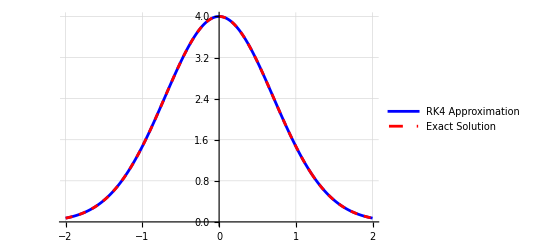

```mathematica
ListLinePlot[{RK4Results, Transpose[{xSol, ySol}]}, 
  PlotStyle -> {Blue, {Dashed, Red}},
  GridLines -> Automatic, 
  PlotLegends -> {"RK4 Approximation", "Exact Solution"},
  FrameLabel -> {"x", "y"}, LabelStyle -> {Bold, 14}
]
```

📌 Blue Line : RK4 approximation
📌 Dashed Line : Exact solution
📌 Goal : Assess accuracy visually

## 🎯 Conclusion

✅ RK4 provides significantly higher accuracy compared to Euler’s method with a manageable computational cost.
🔬 By incorporating four slope evaluations per step, RK4 minimizes truncation errors.
🚀 It achieves better stability and precision, making it ideal for solving ODEs efficiently.
📈 While slightly more complex, RK4 balances accuracy and efficiency, making it a preferred choice for many applications.